# Plot testing code

## Version: 1.2.4

```mathematica
" 
Mathematica-ported version of the data processing and plot generation code. Current implementation includes the core data extraction and plotting, more in-depth analysis will have to wait until I figure out how filtering works on Mathematica.
"
```

## Directory setting

```mathematica
" 
Find file directory, then use that to navigate to data directory. Will work on any filesystem organized in accordance to current data organization protocol
"
```

```mathematica
currentDir=NotebookDirectory[];
SetDirectory[currentDir];
importdir="../../python/ant/data/trajectories/";
```

## File import

```mathematica
filename="2020072013pooldata";
hdf5File=Import[ToString@Row@{importdir,filename,".hdf5"},"Data"];
Needs["ErrorBarPlots`"]
```

## Recording Parameters

```mathematica
" 
Parameters from experiment recording. Upgrade this later to automatically import the values from a params file to ensure human error doesn't mess up calculations
"
```

```mathematica
size=17.5;
framerate=10;
trajLen=18000;
boundary=2;
```

## Functions

### I. Position array

```mathematica
" There is a problem where there is missing data (NaN) and Mathematica fails to handle NaN because that's not a recognized object. For now, temporary patch is to simply average over previous subsequent values, but this will fail when multiple successive points are missing data entries. 
"
```

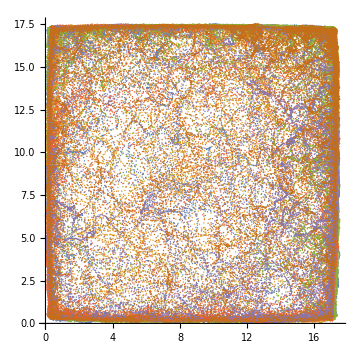

```mathematica
position={};
Module[{x,y,xholes,yholes},
Do[
dset=hdf5File⟦i⟧;
{x,y}=Transpose[dset⟦2;;2+trajLen,1;;2⟧];
Do[If[x⟦i⟧<2,x⟦i⟧=(x⟦i-1⟧+x⟦i-1⟧)/2],{i,1,Length[x]}];
Do[If[y⟦i⟧<2,y⟦i⟧=(y⟦i-1⟧+y⟦i-1⟧)/2],{i,1,Length[y]}];
x=((x-Min[x])size)/(Max[x]-Min[x]);
y=((y-Min[y])size)/(Max[y]-Min[y]);
AppendTo[position,Transpose[{x,y}]];
,{i,1,Length[hdf5File]}]];ListPlot[position,AspectRatio->1,ImageSize->Medium]
```

### II. Velocity array (+ III. Speed array)

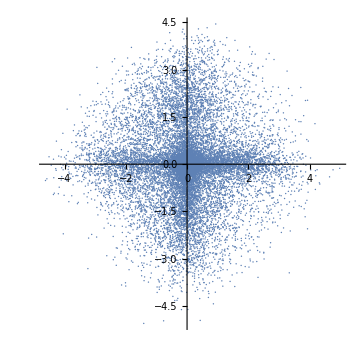

```mathematica
velocity={};
speed={};
Module[{pos,velx,vely,vel,spd},
Do[
pos=Transpose[position⟦i⟧];
velx=Differences[pos⟦1⟧] framerate;
vely=Differences[pos⟦2⟧]framerate;
vel=Transpose[{velx,vely}];
spd=Sqrt[vel⟦;;,1⟧^2+vel⟦;;,2⟧^2];
AppendTo[velocity,vel];
AppendTo[speed,spd];
,{i,1,Length[hdf5File]}]];ListPlot[velocity⟦1⟧,AspectRatio->1,ImageSize->Medium]
```

### III. Orientation array

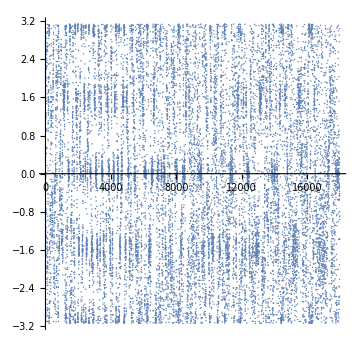

```mathematica
orientation={};
ct=0;
Module[{velx,vely,orr},
Do[
{velx,vely}=Transpose[velocity⟦i⟧];
orr=ArcTan[velx,vely]+π;
(*Do[
If[Abs[orr⟦k⟧-orr⟦k-1⟧]>π,
orr⟦k⟧=Mod[orr⟦k⟧-π,2.π]];
ct+=1;
,{k,2,Length[orr]}];*)
AppendTo[orientation,orr-π];
,{i,1,Length[hdf5File]}]];ListPlot[orientation⟦1⟧,AspectRatio->1,ImageSize->Medium]
```

### IV. Angular velocity array

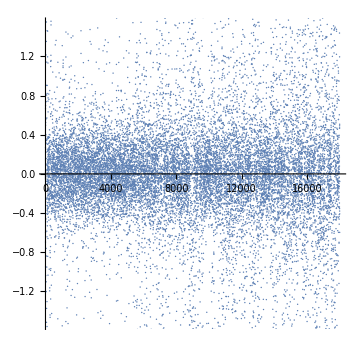

```mathematica
angularVelocity={};
Module[{orr,av},
Do[
orr=orientation⟦i⟧;
av=Mod[Differences[orr]+π,2.π]-π;
AppendTo[angularVelocity,av]
,{i,1,Length[hdf5File]}]];ListPlot[angularVelocity⟦1⟧,AspectRatio->1,ImageSize->Medium]
```

### IV. Acceleration array

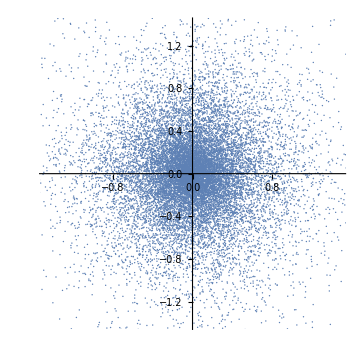

```mathematica
acceleration={};
Module[{velx,vely,accx,accy},
Do[
{velx,vely}=Transpose[velocity⟦i⟧];
accx=Differences[velx];
accy=Differences[vely];
AppendTo[acceleration,Transpose[{accx,accy}]];
,{i,1,Length[hdf5File]}]];ListPlot[acceleration⟦1⟧,AspectRatio->1,ImageSize->Medium]
```

## Analyses

### Symmetry check

```mathematica
" This Block adds up the values of Orientation and Angular velocity over datasets and timesteps; if distribution is indeed symmetric, the sum must evaluate to zero";
```

```mathematica
orrSum=Sum[orientation⟦i,j⟧,{i,1,Length[hdf5File]},{j,1,trajLen-1}]
```

-4157.37

```mathematica
avSum=Sum[angularVelocity⟦i,j⟧,{i,1,Length[hdf5File]},{j,1,trajLen-2}]
```

-470.777

```mathematica
" Sums are very far from zero ";
```

### Data filtering by distance from boundary

```mathematica
boundaryMask={};
Module[{mask},
mask={};mask=Position[position⟦;;,2;;-2⟧,_?(((#⟦1⟧>boundary ∧#⟦2⟧>boundary)∧(#⟦1⟧<size-boundary∧#⟦2⟧<size-boundary))&),{2},Heads->False];
boundaryMask=mask;
]
positionF=position⟦#⟦1⟧,#⟦2⟧⟧&/@boundaryMask;
angularVelocityF=angularVelocity⟦#⟦1⟧,#⟦2⟧⟧&/@boundaryMask;Histogram3D[positionF]
```

-Graphics3D-

## Generate Histogram

### 2D-Histogram

```mathematica
" Valid variables: speed, orientation, angular velocity ";
```

#### Plot config

```mathematica
data=rescaled;
samplesize=0;
Do[
samplesize+=Length[data⟦i⟧]
,{i,1,Length[data]}];
If[samplesize==0,
samplesize=Length[data]];
flatten=False;
axesLabel={"Orientation (rad)","Probability density"};
bincounts=150;
angularticks=True;
```

#### Plot generation

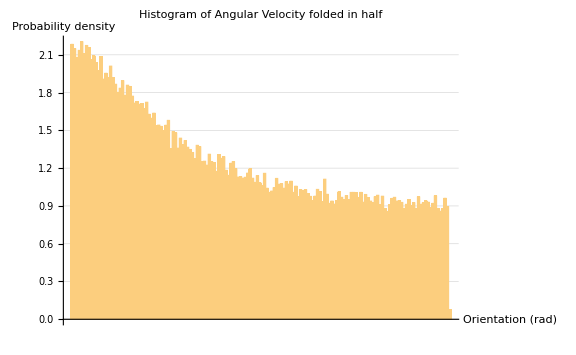

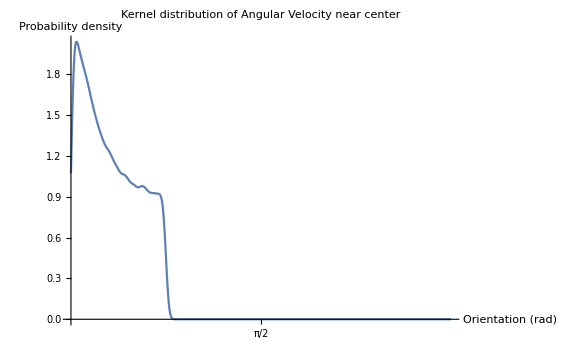

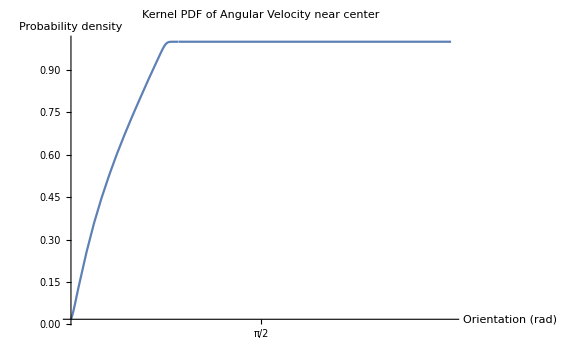

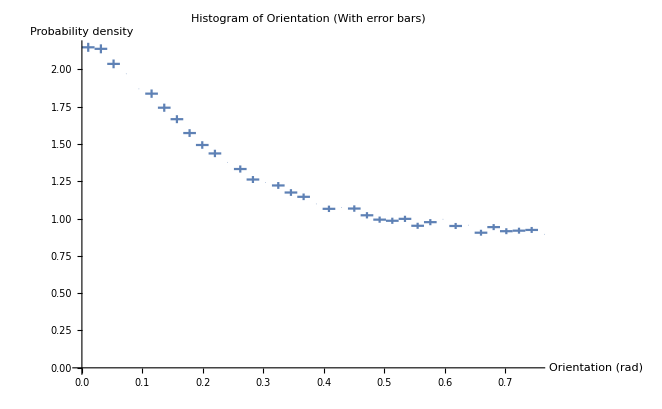

```mathematica
If[flatten,data=Flatten[data]];
range={Min[data],Max[data]};
If[angularticks,
ticks={Range[-2π,2π,π/8],Automatic},
ticks=Automatic];

err={};
Do[
AppendTo[err,ErrorBar[1./(range⟦2⟧-range⟦1⟧),1/Sqrt[samplesize]]];
,{n,1,10}];
dist=SmoothKernelDistribution[data];
Histogram[data,bincounts,"PDF",AxesLabel->axesLabel,PlotRange->Full,ImageSize->Large,Ticks->ticks,GridLines->Automatic,PlotLabel->"Histogram of Angular Velocity folded in half"]
Plot[PDF[dist,x],{x,0,π},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel distribution of Angular Velocity near center"]
Plot[CDF[dist,x],{x,0,π},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel PDF of Angular Velocity near center"]
Module[{temp},temp={};
hist=HistogramList[data,{π/bincounts},"PDF"];
len=Length[hist⟦1⟧];
errors={};
Do[
AppendTo[temp,(hist⟦1,i⟧+hist⟦1,i+1⟧)/2.];
binwidth=π/bincounts;
AppendTo[errors,ErrorBar[binwidth/2.,Sqrt[hist⟦2,i⟧(1-hist⟦2,i⟧binwidth)/(Length[data]binwidth)]]]
,{i,1,Length[hist⟦2⟧]}];
hist={temp,hist⟦2⟧};
copy=histᵀ;
hist=Partition[Riffle[histᵀ,errors],2];
];
ErrorListPlot[hist,PlotRange->{{0,0.75},Full},AxesLabel->axesLabel,PlotLabel->"Histogram of Orientation (With error bars)",PlotStyle->PointSize[0]]
```

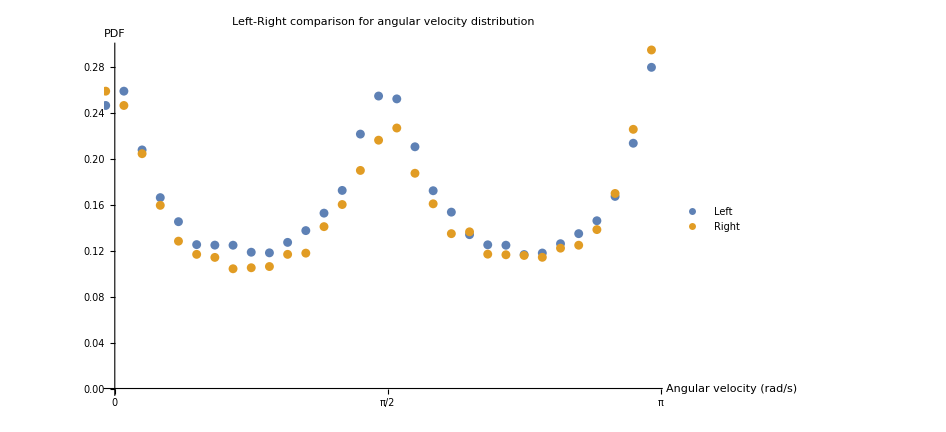

```mathematica
(*mirror=[-copyᵀ⟦1⟧,Reverse[copyᵀ⟦2⟧];*)
sym=ListPlot[{{ -copyᵀ⟦1⟧,copyᵀ⟦2⟧}ᵀ,copy},PlotRange->{{0,Automatic},Full},PlotLabel->"Left-Right comparison for angular velocity distribution",PlotLegends->{"Left","Right"},ImageSize->700,Ticks->ticks,AxesLabel->{"Angular velocity (rad/s)", "PDF"}]
```

```mathematica
Export["Angularvelocitysymmetrycheck.png",sym]
```

Angularvelocitysymmetrycheck.png

### Orientation symmetry check

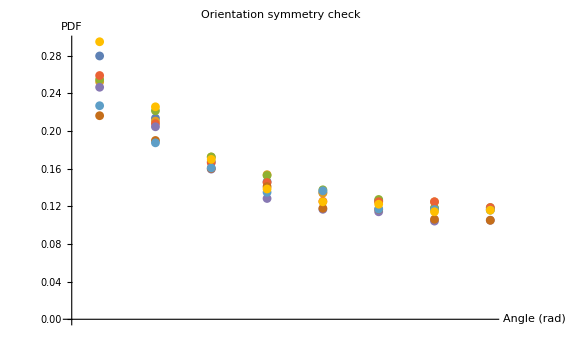

```mathematica
orr=ListPlot[Table[Block[{a=Select[copy,-π+((i-1) π)/4≤#⟦1⟧≤-π+(π i)/4&]},
({(-1)^(i+1)(#⟦1⟧-(i π)/4+(9π)/8)+π/8,#⟦2⟧}&/@aᵀ)ᵀ
],{i,1,8}],AxesLabel->{"Angle (rad)", "PDF"},Ticks->ticks,ImageSize->Large,PlotLabel->"Orientation symmetry check"]
```

```mathematica
Export["Orientationsymmetrycheck.png",orr]
```

Orientationsymmetrycheck.png

```mathematica
CentralMoment[data,3]
CentralMoment[data,2]
CentralMoment[data,4]
```

0.337094

3.43392

21.4791

```mathematica
dimensionfree=CentralMoment[data,3]/(CentralMoment[data,2])^(3/2) (* Used 2nd moment here because mean is zero; this division is needed because then scale factor affects value of moments *)
```

0.0529743

```mathematica
wrap2=data;
```

```mathematica
wraplength=Length[wrap2]/8;
wrap=wrap2⟦wraplength+1;;⟧;
wrap=AppendTo[wrap,wrap2⟦;;wraplength⟧];
wrap2=Flatten[wrap];
```

```mathematica
dimensionfree=CentralMoment[wrap2,3]/(CentralMoment[wrap2,2])^(3/2)
wrap2⟦1⟧
```

0.0529743

0.840967

```mathematica
Dimensions[wrap2]
```

{108000}

```mathematica
{0.053,0.053,0.052,0.48,0.45,0.72,0.88,0.91};
```

```mathematica
(* For oreintation, do the central moment calculation 4 times over 2 peaks and 2 troughs, make sure to wrap data around *)
```

```mathematica
data⟦2⟧
```

-1.21807

```mathematica
Dimensions[wrap]
```

{108001}

### 3D-Histogram

```mathematica
" Valid variables: Position, velocity, acceleration ";
```

#### Plot config

```mathematica
data3d=position;
flatten=True;
axesLabel={"x (cm)","y (cm)","Frequency"};
angularticks=False;
bincounts=8;
```

#### Plot generation

-Graphics3D-

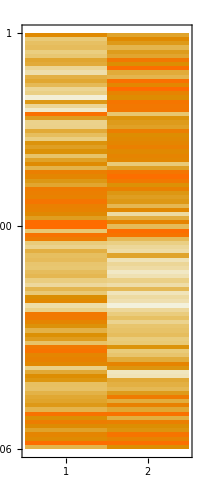

```mathematica
If[flatten,data3d=Flatten[data3d,1];flatten=False];
If[angularticks,
ticks={Range[-2π,2π,π/4],Automatic},
ticks=Automatic];
Histogram3D[data3d,{bincounts,bincounts},AxesLabel->axesLabel,PlotRange->{{Min[data3d],Max[data3d]},{Min[data3d],Max[data3d]},Automatic},ImageSize->Large,Ticks->ticks]
MatrixPlot[data3d]
```

#### Polar plot

```mathematica
ListPolarPlot[angularVelocityF]
```

ListPolarPlot::lpn: angularVelocityF is not a list of numbers or pairs of numbers.

ListPolarPlot[angularVelocityF]

```mathematica
1.copy
```

{{-3.06305,0.260896},{-2.90597,0.179727},{-2.74889,0.144124},{-2.59181,0.127383},{-2.43473,0.118541},{-2.27765,0.121194},{-2.12058,0.128385},{-1.9635,0.146894},{-1.80642,0.180376},{-1.64934,0.243153},{-1.49226,0.249579},{-1.33518,0.183146},{-1.1781,0.148368},{-1.02102,0.130094},{-0.863938,0.119071},{-0.706858,0.122137},{-0.549779,0.124789},{-0.392699,0.138995},{-0.235619,0.174658},{-0.0785398,0.247515},{0.0785398,0.236846},{0.235619,0.170355},{0.392699,0.127796},{0.549779,0.11188},{0.706858,0.10351},{0.863938,0.107046},{1.02102,0.115888},{1.1781,0.134692},{1.33518,0.170178},{1.49226,0.207609},{1.64934,0.217689},{1.80642,0.165934},{1.9635,0.137816},{2.12058,0.121194},{2.27765,0.116537},{2.43473,0.114651},{2.59181,0.120899},{2.74889,0.136166},{2.90597,0.180906},{3.06305,0.279582}}

```mathematica
maxScale=1.1;
angleDivisions=bincounts;
dAng=(2. π)/(angleDivisions+1);
ccopy={copyᵀ⟦1⟧,copyᵀ⟦2⟧}ᵀ;
ListPolarPlot[{{0,maxScale}},PolarAxes->True,PolarGridLines->Automatic,PolarTicks->{"Radians",Automatic},PlotStyle->{None},Epilog->{Opacity[0.7],Blue,Table[Disk[{0,0}, ccopyᵀ⟦2,ang⟧,{ccopyᵀ⟦1,ang⟧-dAng/2.,ccopyᵀ⟦1,ang⟧+dAng/2.}],{ang,1,angleDivisions}]},PlotLabel->"Polar histogram of angular velocity in linear scales\n"]
```

-Graphics-

```mathematica
1.ccopy⟦angleDivisions+2⟧
```

{-1.64934,0.243153}

```mathematica
SectorChart[copy,PolarGridLines->Automatic,PolarTicks->{Automatic,None},PolarAxes->{True,False},SectorOrigin->0]
```

-Graphics-

```mathematica
Dimensions[hist]
```

{40,2}

```mathematica
copy⟦1⟧
```

{-3.06305,0.260896}

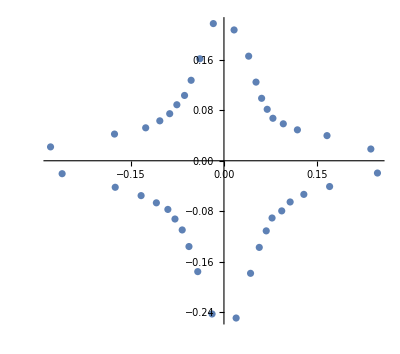

```mathematica
ListPolarPlot[copy]
```

```mathematica
bb=HistogramList[dd];
```

HistogramList::ldata: dd is not a valid dataset or list of datasets.

```mathematica
Dimensions[bb⟦2⟧]
```

Part::partw: Part 2 of HistogramList[dd] does not exist.

{2}

```mathematica
MatrixPlot@bb
```

MatrixPlot::mat0: Argument HistogramList[dd] at position 1 is not a matrix.

MatrixPlot[HistogramList[dd]]

```mathematica
dd=data3dᵀ⟦1⟧;
```

```mathematica
Dimensions[bb⟦⟧]
```

{2}

```mathematica
HistogramList
```

HistogramList

```mathematica
Dimensions[data3d]
```

{108006,2}

```mathematica
binsize=17.5/bincounts+0.01;
thing =BinCounts[data3d,binsize,binsize];
Dimensions[thing]
```

{9,9}

```mathematica
thing=Drop[thing,1];
Do[
thing⟦j⟧=Drop[thing⟦j⟧,1]
,{j,1,Length[thing]}]
```

```mathematica
thing=thing/Length[data3d];
```

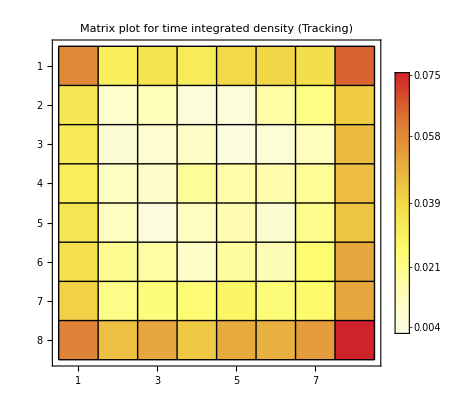

```mathematica
out=Show[MatrixPlot[thing,PlotLegends->Automatic,ColorFunction->"TemperatureMap",Mesh->True,MeshStyle->Thin,PlotLabel->"Matrix plot for time integrated density (Tracking)"]]
```

```mathematica
Export["outtr.png",out]
```

outtr.png

```mathematica
thing⟦1⟧=1
```

1

```mathematica
Max[data3d]
```

17.5

```mathematica
17.5/8
```

2.1875

```mathematica
Total@Total@thing
```

316291/36002

## Model fitting

### Gaussian

```mathematica
gaus={a Exp[(-(x)^2)/(2 b^2)],a>0,b>0};
nlm=NonlinearModelFit[copy, gaus, {a,b}, x];
```

NonlinearModelFit::ivar: … is not a valid variable.

```mathematica
Plot[nlm[x],{x,-π,π},PlotRange->Full]
```

NonlinearModelFit::ivar: … is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

-Graphics-

NonlinearModelFit::ivar: … is not a valid variable.

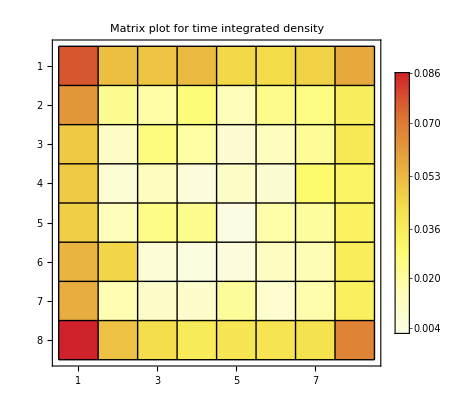
NonlinearModelFit[Transpose[{Mod[3.14159+meh,6.28319],Log[100. Transpose[meh]⟦2⟧]}],{ⅇ^(-x^2/(2 b^2)) -Graphics-,-Graphics->0,b>0},{-Graphics-,b},x]

```mathematica
nlm
```

```mathematica
s=Sqrt[(1/2)/1.59468]
```

0.559949

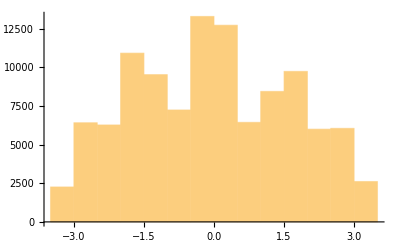

```mathematica
Histogram@Flatten[orientation]
```

```mathematica
Min[orientation]
```

-1.5708

```mathematica
ct
```

0

## Using syemmetry to fold data

### Orientation

```mathematica
rescaled=Flatten@Table[Block[{a=Select[data,-π+((i-1) π)/4≤#≤-π+(π i)/4&]},
((-1)^(i+1)(#-(i π)/4+(9π)/8)+π/8)&/@a
],{i,1,8}];
```

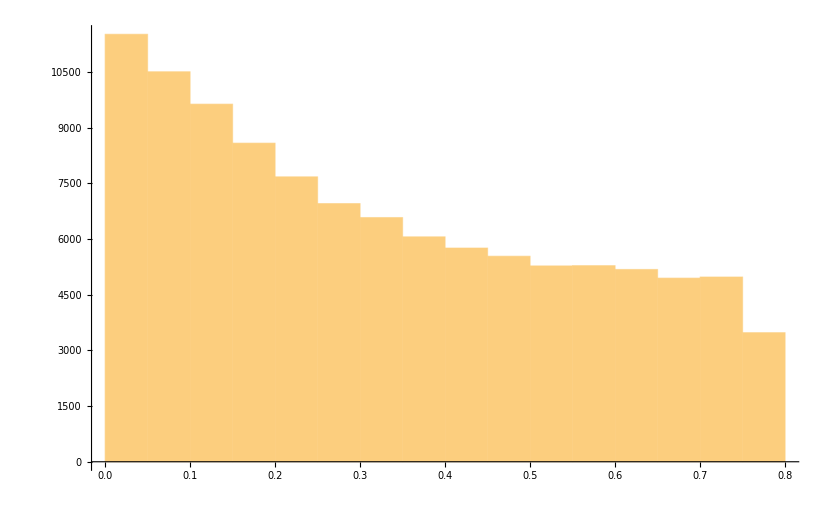

```mathematica
Histogram@rescaled
```

### Angular velocity

```mathematica
angularrescaled=Abs[data];
```

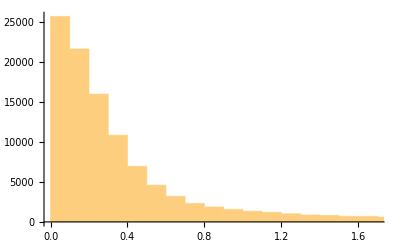

```mathematica
Histogram@angularrescaled
```

```mathematica
hist
```

{{{0.0314159,2.41443},ErrorBar[0.0628319,0.+0.0447494 ⅈ]},{{0.0942478,2.24627},ErrorBar[0.0628319,0.+0.0405161 ⅈ]},{{0.15708,1.96715},ErrorBar[0.0628319,0.+0.0334006 ⅈ]},{{0.219911,1.64543},ErrorBar[0.0628319,0.+0.0249548 ⅈ]},{{0.282743,1.30721},ErrorBar[0.0628319,0.+0.0153454 ⅈ]},{{0.345575,1.03073},ErrorBar[0.0628319,0.+0.00430988 ⅈ]},{{0.408407,0.767818},ErrorBar[0.0628319,0.0102243]},{{0.471239,0.574611},ErrorBar[0.0628319,0.0119721]},{{0.534071,0.462459},ErrorBar[0.0628319,0.0120735]},{{0.596903,0.341613},ErrorBar[0.0628319,0.0114841]},{{0.659734,0.283695},ErrorBar[0.0628319,0.010916]},{{0.722566,0.227987},ErrorBar[0.0628319,0.0101592]},{{0.785398,0.199544},ErrorBar[0.0628319,0.00967784]},{{0.84823,0.178175},ErrorBar[0.0628319,0.00926624]},{{0.911062,0.151206},ErrorBar[0.0628319,0.00867512]},{{0.973894,0.138384},ErrorBar[0.0628319,0.00836162]},{{1.03673,0.12851},ErrorBar[0.0628319,0.00810382]},{{1.09956,0.112004},ErrorBar[0.0628319,0.00763683]},{{1.16239,0.108615},ErrorBar[0.0628319,0.00753472]},{{1.22522,0.100067},ErrorBar[0.0628319,0.00726676]},{{1.28805,0.0873927},ErrorBar[0.0628319,0.00683864]},{{1.35088,0.077666},ErrorBar[0.0628319,0.00648112]},{{1.41372,0.0753081},ErrorBar[0.0628319,0.00639013]},{{1.47655,0.0745712},ErrorBar[0.0628319,0.00636132]},{{1.53938,0.0674972},ErrorBar[0.0628319,0.00607517]},{{1.60221,0.0585074},ErrorBar[0.0628319,0.00568335]},{{1.66504,0.0657287},ErrorBar[0.0628319,0.00600074]},{{1.72788,0.0557073},ErrorBar[0.0628319,0.00555392]},{{1.79071,0.0552652},ErrorBar[0.0628319,0.00553313]},{{1.85354,0.0526125},ErrorBar[0.0628319,0.00540628]},{{1.91637,0.0524651},ErrorBar[0.0628319,0.00539912]},{{1.9792,0.0499597},ErrorBar[0.0628319,0.00527559]},{{2.04204,0.0440648},ErrorBar[0.0628319,0.00496993]},{{2.10487,0.0468649},ErrorBar[0.0628319,0.00511789]},{{2.1677,0.0474544},ErrorBar[0.0628319,0.00514839]},{{2.23053,0.0462754},ErrorBar[0.0628319,0.00508718]},{{2.29336,0.0415594},ErrorBar[0.0628319,0.0048329]},{{2.35619,0.0459806},ErrorBar[0.0628319,0.00507173]},{{2.41903,0.0422963},ErrorBar[0.0628319,0.00487368]},{{2.48186,0.0414121},ErrorBar[0.0628319,0.00482469]},{{2.54469,0.0408226},ErrorBar[0.0628319,0.0047917]},{{2.60752,0.0452438},ErrorBar[0.0628319,0.00503287]},{{2.67035,0.0384646},ErrorBar[0.0628319,0.00465697]},{{2.73319,0.0383172},ErrorBar[0.0628319,0.0046484]},{{2.79602,0.0381698},ErrorBar[0.0628319,0.0046398]},{{2.85885,0.0400857},ErrorBar[0.0628319,0.00475008]},{{2.92168,0.0384646},ErrorBar[0.0628319,0.00465697]},{{2.98451,0.0409699},ErrorBar[0.0628319,0.00479998]},{{3.04734,0.0396436},ErrorBar[0.0628319,0.0047249]},{{3.11018,0.0408226},ErrorBar[0.0628319,0.0047917]}}

```mathematica
Length[data]
```

107994

```mathematica
hist⟦1⟧
```

{{0.0314159,2.41443},ErrorBar[0.0628319,0.+0.0447494 ⅈ]}

```mathematica
hist=HistogramList[data,{(1.π)/bincounts},"PDF"] binwidth
```

{{0.,0.00789568,0.0157914,0.0236871,0.0315827,0.0394784,0.0473741,0.0552698,0.0631655,0.0710612,0.0789568,0.0868525,0.0947482,0.102644,0.11054,0.118435,0.126331,0.134227,0.142122,0.150018,0.157914,0.165809,0.173705,0.181601,0.189496,0.197392,0.205288,0.213183,0.221079,0.228975,0.236871,0.244766,0.252662,0.260558,0.268453,0.276349,0.284245,0.29214,0.300036,0.307932,0.315827,0.323723,0.331619,0.339514,0.34741,0.355306,0.363201,0.371097,0.378993,0.386888,0.394784},{0.303406,0.282275,0.247199,0.206771,0.164268,0.129526,0.0964868,0.0722077,0.0581143,0.0429283,0.0356501,0.0286497,0.0250755,0.0223901,0.0190011,0.0173899,0.016149,0.0140749,0.0136489,0.0125748,0.0109821,0.0097598,0.00946349,0.00937089,0.00848195,0.00735226,0.00825972,0.00700039,0.00694483,0.00661148,0.00659296,0.00627813,0.00553734,0.00588922,0.00596329,0.00581514,0.00522251,0.0057781,0.00531511,0.00520399,0.00512991,0.0056855,0.0048336,0.00481508,0.00479656,0.00503732,0.0048336,0.00514843,0.00498176,0.00512991}}

```mathematica
meh={1,22,3,4,5};
```

```mathematica
meh⟦3;;5⟧
```

{3,4,5}

```mathematica
beh=meh⟦4;;⟧;
beh=AppendTo[beh,meh⟦;;3⟧];
meh=Flatten[beh]
```

{5,1,22,3,4}